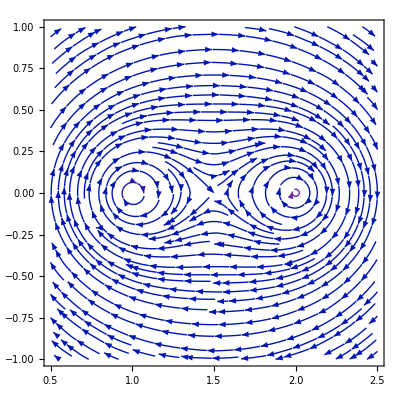

```mathematica
a:=2;
f[x_]:=-{x[[1]],x[[2]]}/(x[[1]]^2+x[[2]]^2);
g3[x_]:=f[{-x[[2]],x[[1]]-1}]+f[{-x[[2]],x[[1]]-2}];(*centered around x=1.5*)
g1[x_]:=f[{-x[[2]],x[[1]]-1}]+f[{-x[[2]],x[[1]]+1}]; (*centered around the origin*)
StreamPlot[g3[{x,y}],{x,0.5,2.5},{y,-1,1}, StreamPoints->Fine]
```

```mathematica
h[x_]:={-x[[1]]+x[[2]],x[[1]]+x[[2]]};(*Rotation by pi/4 and a little bit of scaling*)
```

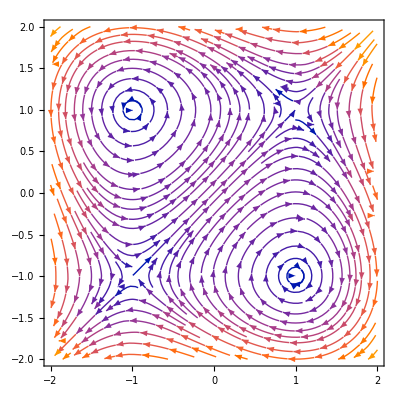

```mathematica
g2[x_]:={-x[[2]]^2+1,-x[[1]]^2+1};
StreamPlot[g2[{x,y}],{x,-a,a},{y,-a,a},StreamPoints->Fine]
```

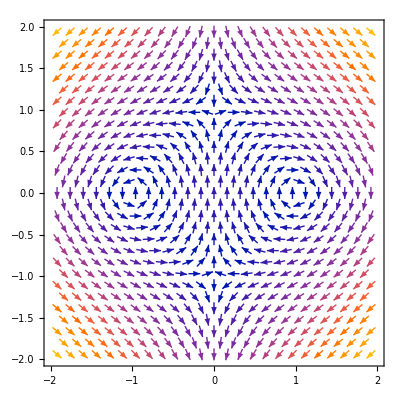

```mathematica
VectorPlot[h[g2[h[{x,y}]]],{x,-a,a},{y,-a,a},VectorPoints->Fine]
```

```mathematica
Animate[StreamPlot[(1-lambda)*h[g2[h[{x,y}]]]+lambda*g1[{x,y}],{x,-a,a},{y,-a,a}, StreamPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```

```mathematica
Animate[VectorPlot[(1-lambda)*h[g2[h[{x,y}]]]+lambda*g1[{x,y}],{x,-a,a},{y,-a,a}, VectorPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```